```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY201/sec_int_data/412nm.dat"]
```

{{1.59376,-0.162342},{1.5163,-0.131408},{1.45822,-0.118705},{1.41492,-0.131727},{1.36475,-0.110139},{1.33366,-0.071453},{1.2821,-0.0524519},{1.25075,-0.0610034},{1.2275,-0.0620669},{1.20277,-0.0553964},{1.18632,-0.0355236},{1.16701,-0.059092},{1.14926,-0.0822735},{1.12973,-0.155321},{1.10588,-2.07688},{1.11907,-0.176546},{1.13878,-0.0895965},{1.30525,-0.14994},{1.35407,-0.223506}}

-1.24611+0.809488 x

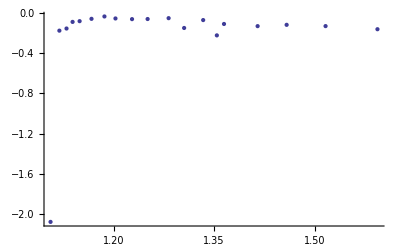

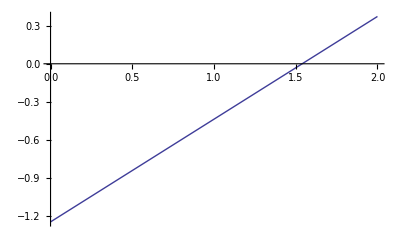

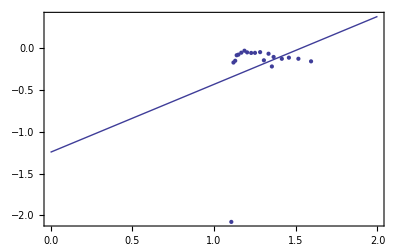

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```